

```mathematica
sinplot=Plot[Sin[x],{x,0,2Pi}]
```

```mathematica
sampledata=Table[Random[],{50},{50}];
```

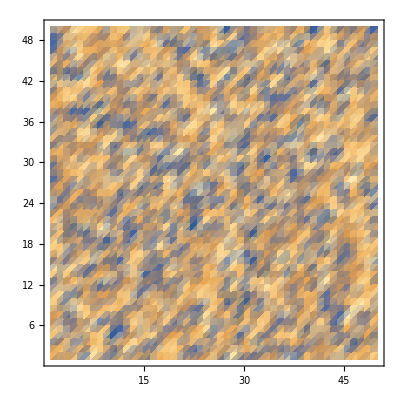

```mathematica
ListDensityPlot[sampledata]
```

```mathematica
Options[Plot,PlotPoints]
```

{PlotPoints→Automatic}

```mathematica
Options[Plot,{MaxBend,PlotDivision}]
```

Options::optnf: MaxBend is not a known option for Plot.

Options::optnf: PlotDivision is not a known option for Plot.

{}

```mathematica
Plot[Sin[x],{x,0,2Pi},
PlotPoints->4,MaxBend->45,
PlotDivision->1]
```

Plot::optx: Unknown option MaxBend→45 in Plot[Sin[x],{x,0,2 π},PlotPoints→4,MaxBend→45,PlotDivision→1].

Plot[Sin[x],{x,0,2 π},PlotPoints→4,MaxBend→45,PlotDivision→1]

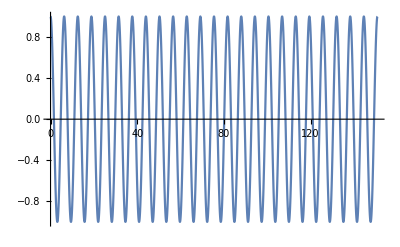

```mathematica
Plot[Cos[x],{x,0,2Pi(24)}]
```

```mathematica
Options[Plot3D,PlotPoints]
```

{PlotPoints→Automatic}

```mathematica
Plot3D[Sin[x y],{x,0,3Pi/2},{y,0,3Pi/2}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,2Pi},{y,0,2Pi}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,2Pi},{y,0,2Pi},PlotPoints->80]
```

-Graphics3D-

```mathematica
Plot3D[1/(1-ArcTan[x y]),{x,0,4},{y,0,4}]
```

-Graphics3D-

```mathematica
atanplot=Plot3D[1/(1-ArcTan[x y]),{x,0,4},{y,0,4},PlotPoints->35]
```

-Graphics3D-

```mathematica
Show[atanplot,ViewPoint->{2.8,0,2}]
```

-Graphics3D-

```mathematica
Options[Plot3D,ViewPoint]
```

{ViewPoint→{1.3,-2.4,2.}}

```mathematica
Options[Plot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,0.4},BoxStyle→{},ClippingStyle→Automatic,ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FaceGrids→None,FaceGridsStyle→{},Filling→None,FillingStyle→Opacity[0.5],FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→Fit,ScalingFunctions→None,SphericalRegion→False,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision}

```mathematica
Show[atanplot,Axes->False,Boxed->False]
```

-Graphics3D-

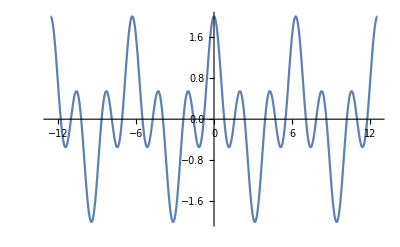

```mathematica
p1=Plot[Cos[x]+Cos[3x],{x,-4Pi,4Pi}]
```

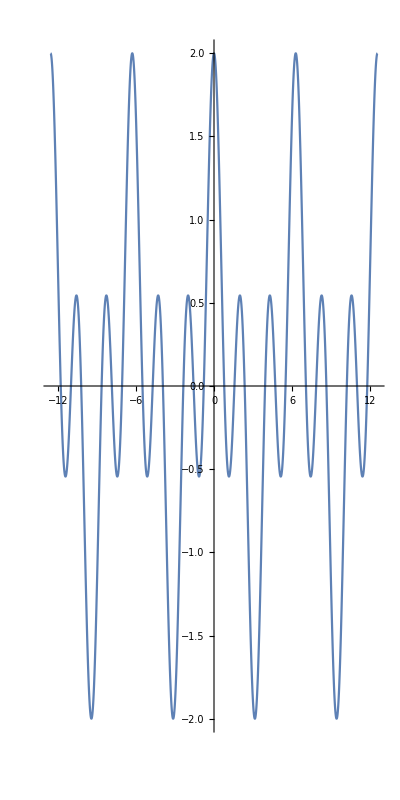

```mathematica
Show[p1,AspectRatio->2]
```

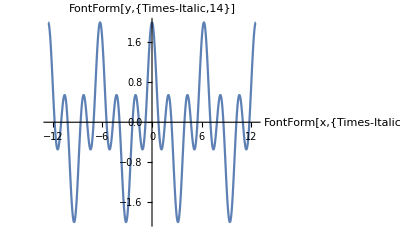

```mathematica
Show[p1,
AxesLabel->{FontForm["x",{"Times-Italic",14}],
FontForm["y",{"Times-Italic",14}]}]
```

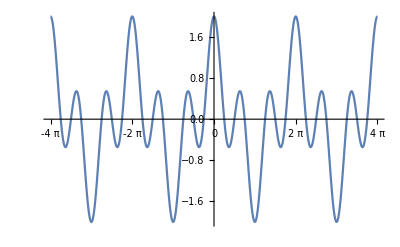

```mathematica
Show[p1,
Ticks->{Range[-4Pi,4Pi,Pi],Automatic},
DefaultFont->{"Helvetica",9}]
```

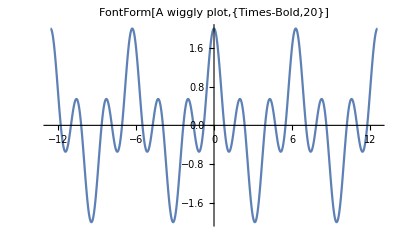

```mathematica
Show[p1,PlotLabel->FontForm["A wiggly plot",
{"Times-Bold",20}]]
```

```mathematica
sinplot=Plot[Sin[x],{x,0,2Pi}]
```

-Graphics-

```mathematica
Show[sinplot,
Graphics[
{Thickness[.001],
Map[Line[{{#[[1]],0},#}]&,
Nest[First,sinplot,4]]}]]
```

-Graphics-

```mathematica
splot=Plot[Sin[x],{x,-2Pi,2Pi}];
```

```mathematica
Show[splot/.{x_?NumberQ,y_?NumberQ}->{y,x}]
```

Part::partw: Part 2 of #1 does not exist.

-Graphics-

```mathematica
rotatePlot[p_Graphics,theta_]:=
Show[p/.{x_?NumberQ,y_?NumberQ}->
{x,y}.{{Cos[theta],Sin[theta]},
{-Sin[theta],Cos[theta]}}]
```

```mathematica
plot1=Plot[Sin[x],{x,0,2Pi}]
```

-Graphics-

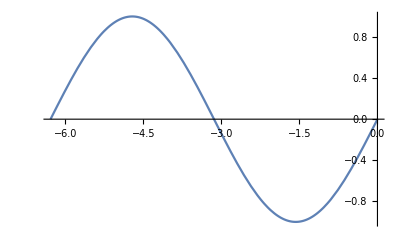

```mathematica
rotatePlot[plot1,Pi]
```

```mathematica
f[x_]:=Normal[Series[x+Sin[x],{x,0,5}]]
```

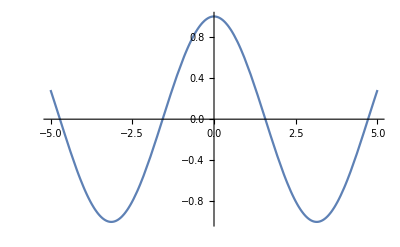

```mathematica
Plot[f[x],{x,-5,5}]
```